4.69733

-0.0127342

{-1.08077,{y→0.212189}}

5.06657

{x→-0.00562313}

{-0.983159,{y→0.220909}}

0.150416

{x→-0.00579004}

{-0.980325,{y→0.221171}}

0.00444761

{x→-0.00579498}

{-0.980241,{y→0.221179}}

0.000131492

{x→-0.00579513}

{-0.980238,{y→0.221179}}

-3.68667×10^-6

{x→-0.00579513}

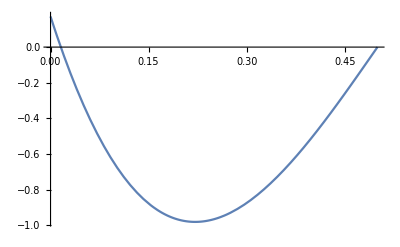

```mathematica
Remove["Global`*"]

EA=2100;

l12[u_,v_]:=(5.5+u)^2+(0.5-v)^2;
l22[u_,v_]:=(4-u)^2+(0.5-v)^2;



Fx1[u_,v_]:=(5.5+u)/Sqrt[l12[u,v]]*EA*1/2*Log[l12[u,v]/30.5]
Fx2[u_,v_]:=(u-4)/Sqrt[l22[u,v]]*EA*1/2*Log[l22[u,v]/16.25]
Fx[u_,v_]:=EA*((5.5+u)/Sqrt[l12[u,v]]*1/2*Log[l12[u,v]/30.5]+(u-4)/Sqrt[l22[u,v]]*1/2*Log[l22[u,v]/16.25])

Fy[u_,v_]:=EA*((0.5-v)/Sqrt[l12[u,v]]*1/2*Log[l12[u,v]/30.5]+(0.5-v)/Sqrt[l22[u,v]]*1/2*Log[l22[u,v]/16.25])



u1 = 0.01009927;
v1 = -0.02552811;

Fx1[u1,v1]
Fy[u1,v1]

FindMinimum[Fy[0,y],{y,0.1}]
Fx[0,0.212189]
FindRoot[Fx[x,0.212189],{x, -0.1}]

FindMinimum[Fy[-0.00562313,y],{y,0.2}]
Fx[-0.00562313,0.220909]
FindRoot[Fx[x,0.220909],{x, -0.1}]

FindMinimum[Fy[-0.00579004,y],{y,0.2}]
Fx[-0.00579004,0.221171]
FindRoot[Fx[x,0.221171],{x, -0.1}]

FindMinimum[Fy[-0.00579498,y],{y,0.2}]
Fx[-0.00579498,0.221179]
FindRoot[Fx[x,0.221179],{x, -0.1}]

FindMinimum[Fy[-0.00579513,y],{y,0.2}]
Fx[-0.00579513,0.221179]
FindRoot[Fx[x,0.221179],{x, -0.1}]

Plot[Fy[-0.00579513,y],{y,0,0.5}]
```

```mathematica
(* Checking strain of solution *)


Log[l12[-0.00579513,0.221179]/30.5]
Log[l22[-0.00579513,0.221179]/16.25]
```

```mathematica
(* deritives *)

D[Fx[u,v],u]
D[Fx[u,v],v]

D[Fy[u,v],u]
D[Fy[u,v],v]
```

```mathematica
(* check python disp. *)

Fx[-0.0003308, -0.00987019]
Fy[-0.0003308, -0.00987019]

u1 = -0.00549649;
v1 = 0.20574372;
Fx[u1, v1]
Fy[u1, v1]
```

-0.591284

0.123123

1.84126×10^-6

-0.981018

```mathematica
(* Clear output *)

NotebookFind[SelectedNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]]
```